# Various Potential Analysis

```mathematica
Needs["PlotLegends`"];
SetDirectory[FileNameJoin[{NotebookDirectory[]}]];
fsTitle=36;
fsAxesLabel=24;
fs2=18;
```

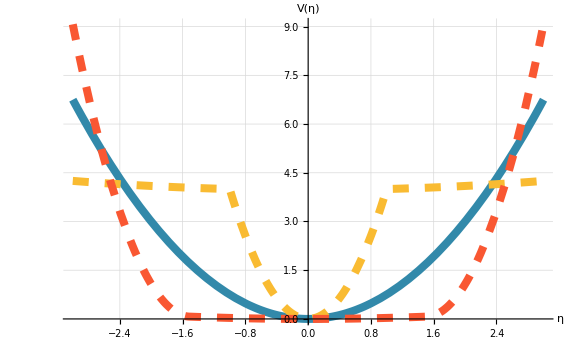

```mathematica
α=1.0;
α2=1.5;

Hσ=1.5;
SoftHSσ=1/16;
HardHSσ=8;
SoftSHσ=1/16;
HardSHσ=8;

HarmonicPotential[x_,σ_]:=1/2 σ x^2;

constHS=HarmonicPotential[α,HardHSσ]-HarmonicPotential[α,SoftHSσ]
constSH=HarmonicPotential[α2,SoftSHσ]

HardSoftPotential[x_]:=If[Abs[x]≤α,HarmonicPotential[x,HardHSσ],constHS+HarmonicPotential[x,SoftHSσ]]

SoftHardPotential[x_]:=If[x≤-α2,HarmonicPotential[x+α2,HardSHσ]+constSH,
If[x≥α2,HarmonicPotential[x-α2,HardSHσ]+constSH,
HarmonicPotential[x,SoftSHσ]
]
]

Plot[
{HarmonicPotential[x,Hσ],HardSoftPotential[x],SoftHardPotential[x]},{x,-3,3},
ImageSize->Large,
PlotStyle->{
{Thickness[0.01],RGBColor[50/255,137/255,170/255]},{Dashing[0.02],Thickness[0.01],RGBColor[249/255,187/255,50/255]},
{Dashing[0.02],Thickness[0.01],RGBColor[249/255,87/255,50/255]}
},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesLabel->{Style["η",FontSize->fsAxesLabel],Style["V(η)",FontSize->fsAxesLabel]},
LabelStyle->{FontSize->fs2}
]
```